```mathematica
(* Number of qubits needed to factor N using Shor's algorithm *)
$Assumptions={𝒩∈Integers, 𝒩>0};
```

```mathematica
Reduce[{𝒩^2≤ 2^q ≤ 2 𝒩^2,𝒩>0}, q]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{𝒩^2≤2^q≤2 𝒩^2,𝒩>0},q]

```mathematica
Reduce[{𝒩^2≤ 2^q,2^q<2 𝒩^2, 𝒩>0}, q, Reals]
```

𝒩≠0&&𝒩>0&&Log[𝒩^2]/Log[2]≤q<Log[2 𝒩^2]/Log[2]

```mathematica
q[𝒩_]:= Ceiling[(2Log[𝒩])/Log[2]]
```

```mathematica
q[15]
```

8

```mathematica
qv[q_, 𝒩_]:= q<Log[2 𝒩^3]/Log[2]
```

```mathematica
qv[8, 15]
```

True

```mathematica
q[21]
```

9

```mathematica
qv[9, 21]
```

True

```mathematica
Table[{2^n-1, q[2^n-1]}, {n, 1, 20}]
```

{{1,0},{3,4},{7,6},{15,8},{31,10},{63,12},{127,14},{255,16},{511,18},{1023,20},{2047,22},{4095,24},{8191,26},{16383,28},{32767,30},{65535,32},{131071,34},{262143,36},{524287,38},{1048575,40}}

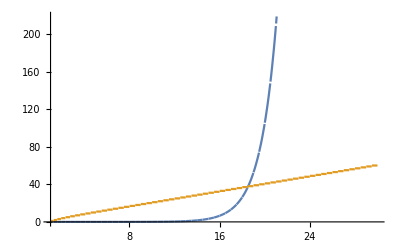

```mathematica
Plot[{(2^n-1)/10000, q[2^n-1]}, {n, 1, 30}, Evaluated-> True]
```